# parabolic mirror focal spot

Image files are from G:\My Drive\Graduate Research\network\parabolic_mirror_alignment

## 2022.10.06

```mathematica
img=-Graphics-;
data=ImageData[img][[;;,;;,1]];
data-=Min[Min[data[[187]]],Min[data[[;;,184]]]];
data/=Max[data];
{ydim,xdim}=data//Dimensions
xmicrons=Range[0,(xdim-1)/pixPerMicron,1/pixPerMicron];
ymicrons=Range[0,(ydim-1)/pixPerMicron,1/pixPerMicron];
pixPerMicron=31.125/3.45;(*magnification/pixel size*)
xmicrons//Length
```

{369,369}

369

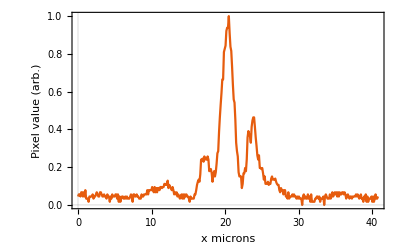

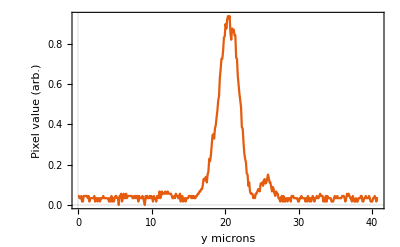

```mathematica
ListPlot[Transpose@{xmicrons,data[[187]]},Joined->True,PlotTheme->"Scientific",FrameLabel->{"x microns","Pixel value (arb.)"},PlotRange->All]
ListPlot[Transpose@{ymicrons,data[[;;,185]]},Joined->True,PlotTheme->"Scientific",FrameLabel->{"y microns","Pixel value (arb.)"},PlotRange->All]
```

```mathematica
xyf=Flatten[Array[{xmicrons[[#2]],ymicrons[[#1]],data[[#1,#2]]}&,data//Dimensions],1];
Image[data]
```

-Graphics-

```mathematica
ListPlot3D[xyf,PlotRange->{0,1},AxesLabel->{"x","y","f"}]
```

-Graphics3D-

```mathematica
filtered=GaussianFilter[data,3];
filtered-=Min[filtered];
filtered/=Max[filtered];
xmic=Reverse[xmicrons];
xyf=Flatten[Array[{xmic[[#2]],ymicrons[[#1]],filtered[[#1,#2]]}&,filtered//Dimensions],1];
ListPlot3D[xyf,PlotRange->{0,1},AxesLabel->{"x","y","f"}]
```

-Graphics3D-

## 2022.09.19

2022.09.19 Image of the mirror focal field taken with the microscope described in my OneNote.

```mathematica
img=-Graphics-;
data=ImageData[(*ColorConvert[*)img(*,"Grayscale"]*)][[;;,;;,1]];
{ydim,xdim}=data//Dimensions
```

{1080,1440}

```mathematica
pixPerMicron=31.125/3.45;(*magnification/pixel size*)
```

```mathematica
xmicrons=Range[0,(xdim-1)/pixPerMicron,1/pixPerMicron];
ymicrons=Range[0,(ydim-1)/pixPerMicron,1/pixPerMicron];
xmicrons//Length
```

1440

```mathematica
xmicrons[[-1]]
```

159.504

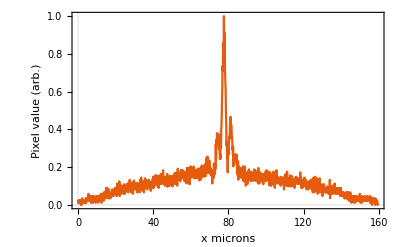

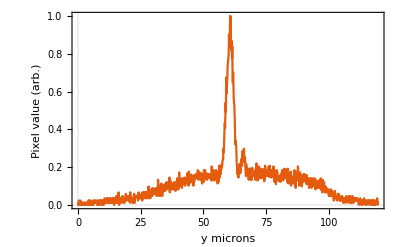

```mathematica
ListPlot[Transpose@{xmicrons,data[[550]]},Joined->True,PlotTheme->"Scientific",FrameLabel->{"x microns","Pixel value (arb.)"},PlotRange->All]
ListPlot[Transpose@{ymicrons,data[[;;,701]]},Joined->True,PlotTheme->"Scientific",FrameLabel->{"y microns","Pixel value (arb.)"},PlotRange->All]
```

Cropped image:

```mathematica
Min[data]
Max[data]
```

0.0588235

1.

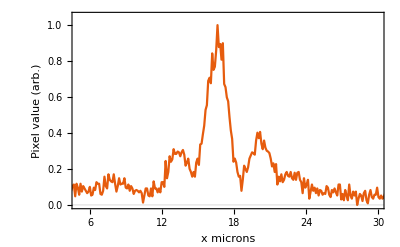

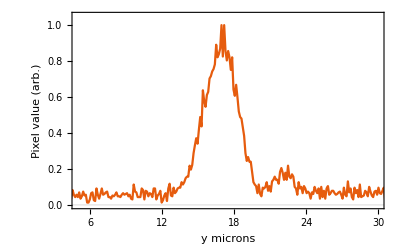

```mathematica
img=-Graphics-;
data=ImageData[img][[;;,;;,1]];
data-=Min[Min[data[[151]]],Min[data[[;;,156]]]];
data/=Max[data];
{ydim,xdim}=data//Dimensions;
xmicrons=Range[0,(xdim-1)/pixPerMicron,1/pixPerMicron];
ymicrons=Range[0,(ydim-1)/pixPerMicron,1/pixPerMicron];
(*ListPlot[Table[Transpose@{xmicrons,data[[155+i]]},{i,Range[-3,3]}],Joined->True,PlotTheme->"Scientific",FrameLabel->{"x microns","Pixel value (arb.)"},PlotRange->{{5,30},{0,1}}]
ListPlot[Table[Transpose@{ymicrons,data[[;;,150+i]]},{i,Range[-3,3]}],Joined->True,PlotTheme->"Scientific",FrameLabel->{"y microns","Pixel value (arb.)"},PlotRange->{{5,30},{0,1}},PlotLegends->Range[-3,3]]*)
ListPlot[Transpose@{xmicrons,data[[156]]},Joined->True,PlotTheme->"Scientific",FrameLabel->{"x microns","Pixel value (arb.)"},PlotRange->{{5,30},{0,1.05}}]
ListPlot[Transpose@{ymicrons,data[[;;,151]]},Joined->True,PlotTheme->"Scientific",FrameLabel->{"y microns","Pixel value (arb.)"},PlotRange->{{5,30},{0,1.05}}]
```

```mathematica
xyf=Flatten[Array[{xmicrons[[#2]],ymicrons[[#1]],data[[#1,#2]]}&,data//Dimensions],1];
Image[data]
```

-Graphics-

```mathematica
ListPlot3D[xyf,PlotRange->{0,1},AxesLabel->{"x","y","f"}]
```

-Graphics3D-

```mathematica
filtered=GaussianFilter[data,10];
filtered-=Min[filtered];
filtered/=Max[filtered];
xyf=Flatten[Array[{xmicrons[[#2]],ymicrons[[#1]],filtered[[#1,#2]]}&,filtered//Dimensions],1];
ListPlot3D[xyf,PlotRange->{0,1},AxesLabel->{"x","y","f"}]
```

-Graphics3D-

```mathematica
model=a Exp[(-2(x-x0)^2)/wx^2]Exp[(-2(y-y0)^2)/wy^2];
fit=FindFit[xyf,model,{{a,0.9},{wx,2},{wy,2},{x0,6},{y0,6.5}},{x,y}]
```

{a→0.243829,wx→21.1937,wy→19.9675,x0→6.39547,y0→6.53544}

```mathematica
Plot3D[a Exp[(-2(x-x0)^2)/wx^2]Exp[(-2(y-y0)^2)/wy^2]/.{a->1,wx->1,wy->1,x0->6.395471826750817,y0->6.535445009759205},{x,0,12},{y,0,12},PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Plot3D[model/.fit,{x,0,12},{y,0,12},PlotRange->{0,1}]
```